# Code Appendix

## Data Import

Import metadata such as the position of each of the feeding stations, water station and the corners of the paddock.

```mathematica
rawMetadata=Import["/Users/katjad/Documents/Github/SheepCapstone/Salt6_corners_food locations_collective decision making_March2019.csv"];
```

```mathematica
paddock=rawMetadata[[-4;;-1,-2;;-1]];
feeding=rawMetadata[[2;;11,-2;;-1]];
water=rawMetadata[[12,-2;;-1]];
```

Create a Graphics Boundary of the paddock

```mathematica
paddockRegion=BoundaryDiscretizeGraphics[Polygon[paddock]];metadataGraphic=Graphics[{LightBrown,Polygon[paddock],Darker[Green],Circle[#,30]&/@feeding,Thick,Darker[Blue],Circle[water,50]}];
```

Import the raw GPS data, so the X and Y coordinates as well as the time stamps and IDS.

```mathematica
rawXs=Import["/Users/katjad/Documents/Github/SheepCapstone/xs.csv"];
rawYs=Import["/Users/katjad/Documents/Github/SheepCapstone/ys.csv"];
rawIDs=Import["/Users/katjad/Documents/Github/SheepCapstone/ids.csv"];
rawTs=Import["/Users/katjad/Documents/Github/SheepCapstone/ts.csv"];
rawTsStart=Import["/Users/katjad/Documents/Github/SheepCapstone/period.start.idxs.csv"];
```

The dataset has 51 sheep(+header) and 210352 time steps

```mathematica
Dimensions[rawXs]
```

{52,210352}

Create two versions of the coordinates, one with missing data as Missing[] for more computational tasks and one with missing data as “Indeterminate” for mathematical tasks

```mathematica
rawCoordinates=Table[{rawXs[[x,y]],rawYs[[x,y]]},{x,2,52},{y,2,210352}]/."NA"->Missing[];
```

```mathematica
rawCoordinates2=rawCoordinates/.Missing[]->Indeterminate
```

{1}
 |  |  |  |

## Distribution of distances

### Individual Sheep

Function to determine the distance between sheep a and b

```mathematica
distances[a_,b_]:=Sqrt[Total[(rawCoordinates2[[a]] - rawCoordinates2[[b]])^2,{2}]]
```

Running this on two sheep will yield the distance they are from each other at each time step

```mathematica
distances[2,4]
```

{Indeterminate,6.2241,8.98001,13.3817,17.971,22.3762,28.6324,26.5542,210335,142.027,140.091,137.291,137.158,137.012,138.097,138.566,Indeterminate}
 |  |  |  |

Creates a function that for a given sheep and time finds all other sheep within a specified radius

```mathematica
SingleSheepWithinRadius[radius_,sheep_,time_]:=
If[rawCoordinates[[sheep,time]]==={Missing[],Missing[]},
Missing[],Nearest[DeleteMissing[MapIndexed[#1->#2[[1]]&,rawCoordinates[[All,time]]],1,3],rawCoordinates[[sheep,time]],{All,radius}]]
```

At step 3000, sheep 7 has 3 other sheep with it in less than 50m radius

```mathematica
SingleSheepWithinRadius[50,7,3000]
```

{7,49,12,32}

This allows us to

```mathematica
sheep1herdsize=With[{herd=SingleSheepWithinRadius[100,1,#]},If[MissingQ[herd],Missing[],Length[herd]]]&/@Range[Length[rawCoordinates[[4]]]];
```

24.4138

22

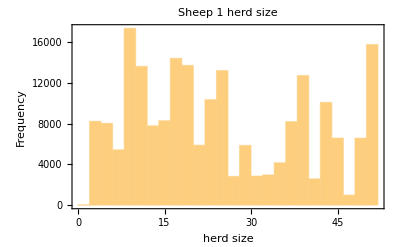

-Graphics-

```mathematica
Mean[DeleteMissing[sheep1herdsize]]//N
Median[DeleteMissing[sheep1herdsize]]
Histogram[sheep1herdsize,PlotLabel->"Sheep 1 herd size",Frame->True,FrameLabel->{"herd size","Frequency"}]
ListLinePlot[sheep1herdsize,PlotLabel->"Sheep 1 herd size over time",Frame->True,FrameLabel->{"time","herd size"}]
```

### Mean over all sheep

Set data Directory to export data to

```mathematica
dataDirectory="/Users/katjad/Documents/Github/SheepCapstone/MXs/DistanceData";
```

Create a function that gets the distances for a pair of sheep and exports the list as an .mx file.

```mathematica
exportDistance[a_,b_]:=
Module[{distance,name},
distance=distances[a,b];
name=StringJoin[ToString[a],"and",ToString[b],".mx"];
Export[FileNameJoin[{dataDirectory,name}],distance]]
```

Generate a list of all the names of the files that were exported.

```mathematica
PairNames=Table[StringJoin[ToString[a],"and",ToString[b],".mx"],{a,1,Length[rawCoordinates2]},{b,a+1,Length[rawCoordinates2]}]
```

Import the data one by one and find the mean and median of each

```mathematica
Module[{currentPairData,data},
data=Table[
currentPairData=DeleteCases[Import[FileNameJoin[{dataDirectory,name}]],Indeterminate];
{Median[currentPairData],Mean[currentPairData]},
{name,Flatten[PairNames]}];
medians=data[[All,1]];
means=data[[All,2]];]
Export[FileNameJoin[{dataDirectory,"medians.mx"}],medians];
Export[FileNameJoin[{dataDirectory,"means.mx"}],means];
```

Median::rectn: Rectangular array of real numbers is expected at position 1 in Median[{Missing[]}].

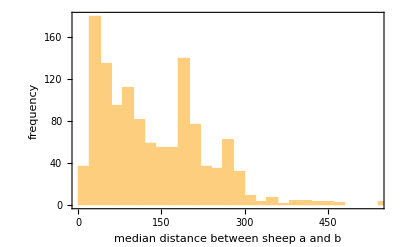

```mathematica
Histogram[medians,Frame->True,FrameLabel->{"median distance between sheep a and b","frequency"}]
```

### Sampling from all pairs

```mathematica
randomDistances=Select[Table[EuclideanDistance@@rawCoordinates2[[RandomInteger[{1,Length[rawCoordinates2]},2],RandomInteger[{1,Length[rawCoordinates2[[1]]]}]]],200000],#>0&]
```

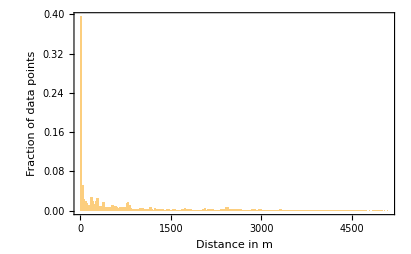

```mathematica
Histogram[randomDistances,{25},"Probability",Frame->True,FrameLabel->{"Distance in m","Fraction of data points"},PlotRange->All]
```

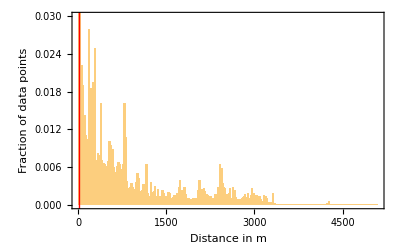

```mathematica
Histogram[randomDistances,{25},"Probability",Frame->True,FrameLabel->{"Distance in m","Fraction of data points"},PlotRange->{All,{0,0.03}},Epilog->{{Red,Thick,InfiniteLine[{{25,0},{25,1}}]}}]
```

```mathematica
Histogram[randomDistances,{50},Frame->True,FrameLabel->{"Distance","count"},ScalingFunctions->{"Log","Log"}]
```

```mathematica
feedingStationsDistances = DeleteCases[Flatten[DistanceMatrix[feeding]//N],0.];
```

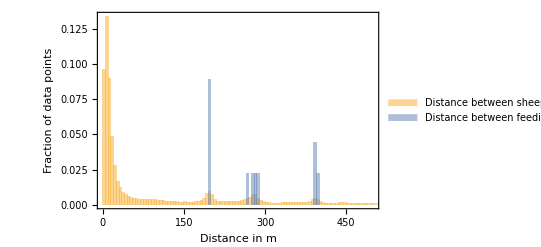

```mathematica
Histogram[{randomDistances,feedingStationsDistances},{5},"Probability",PlotRange->{{0,500},Automatic},Frame->True,FrameLabel-> {"Distance in m","Fraction of data points"},ChartLegends->{"Distance between sheep","Distance between feeding stations"}]
```

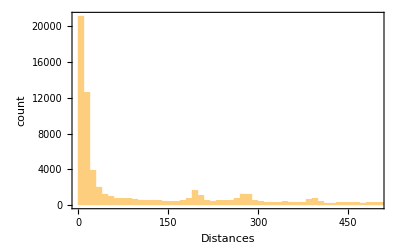

```mathematica
Histogram[randomDistances,{10},PlotRange->{{0,500},All},Frame->True,FrameLabel-> {"Distances","count"}]
```

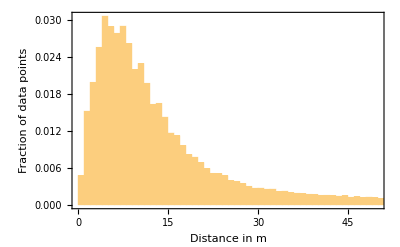

```mathematica
Histogram[randomDistances,{1},"Probability",PlotRange->{{0,50},All},Frame->True,FrameLabel-> {"Distance in m","Fraction of data points"}]
```

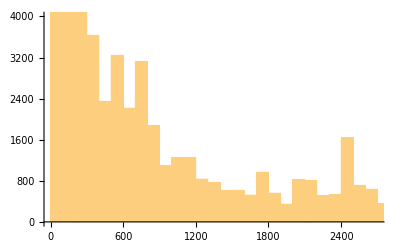

```mathematica
Histogram[randomDistances,PlotRange->{{0,2700},{0,4000}}]
```

## DBSCAN and Clustering

### DBSCAN Implementation

A function that takes a time step and radius and returns a cluster

```mathematica
dbScanClusters[time_,radius_]:=
Module[{positions,rawClusters,outliers},
positions=DeleteMissing[MapIndexed[#1->#2[[1]]&,rawCoordinates[[All,time]]],1,3];
rawClusters=FindClusters[positions,Method->{"DBSCAN","NeighborhoodRadius"->radius,"DropAnomalousValues"->True},DistanceFunction->EuclideanDistance];
outliers=Complement[Values[positions],Flatten[rawClusters]];
Append[rawClusters,outliers]]
```

Plot example radii

```mathematica
dbScanComparison[time_]:=Column[{Show[metadataGraphic,Graphics[Style[Circle[#,50],Thin]&/@DeleteMissing[rawCoordinates[[All,time]],1,2],PlotRange->RegionBounds[paddockRegion]],PlotRange->{{580401.,582573.},{6.562693*^6,6.564282*^6}}],Show[metadataGraphic,ListPlot[FindClusters[DeleteMissing[rawCoordinates[[All,time]],1,2],Method->{"DBSCAN","NeighborhoodRadius"->10},DistanceFunction->EuclideanDistance],AspectRatio->Automatic],PlotRange->{{580401.,582573.},{6.562693*^6,6.564282*^6}}],Show[metadataGraphic,ListPlot[FindClusters[DeleteMissing[rawCoordinates[[All,time]],1,2],Method->{"DBSCAN","NeighborhoodRadius"->30},DistanceFunction->EuclideanDistance],AspectRatio->Automatic],PlotRange->{{580401.,582573.},{6.562693*^6,6.564282*^6}}],
Show[metadataGraphic,ListPlot[FindClusters[DeleteMissing[rawCoordinates[[All,time]],1,2],Method->{"DBSCAN","NeighborhoodRadius"->50},DistanceFunction->EuclideanDistance],AspectRatio->Automatic],PlotRange->{{580401.,582573.},{6.562693*^6,6.564282*^6}}]}]
```

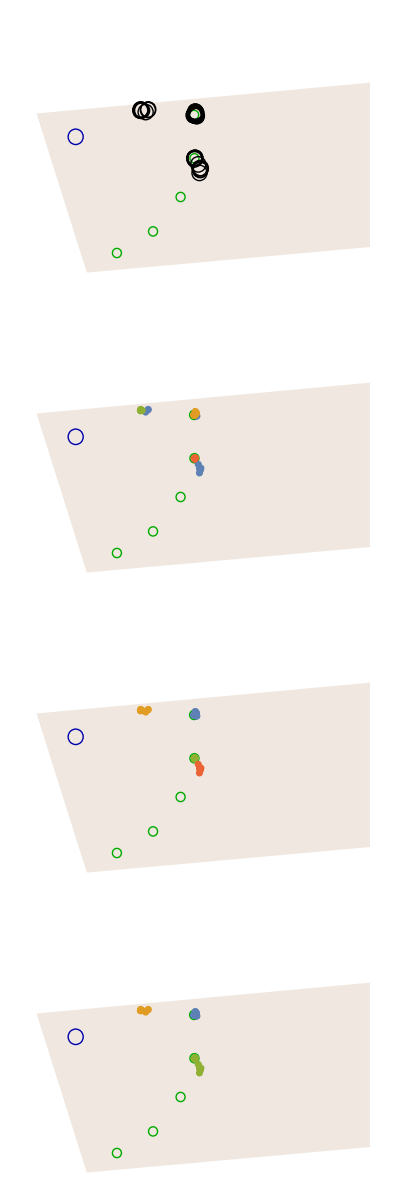

```mathematica
dbScanComparison[1000]
```

### DBSCAN herds production

```mathematica
dbScanHerds5=Table[dbScanClusters[x,5],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds5.mx",dbScanHerds5]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds5.mx

```mathematica
dbScanHerds10=Table[dbScanClusters[x,10],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds10.mx",dbScanHerds10]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds10.mx

```mathematica
dbScanHerds20=Table[dbScanClusters[x,20],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds20.mx",dbScanHerds20]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds20.mx

```mathematica
dbScanHerds30=Table[dbScanClusters[x,30],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds30.mx",dbScanHerds30]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds30.mx

```mathematica
dbScanHerds50=Table[dbScanClusters[x,50],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds50.mx",dbScanHerds50]
```

```mathematica
dbScanHerds100=Table[dbScanClusters[x,100],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds100.mx",dbScanHerds100]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds100.mx

### DBSCAN herds import

```mathematica
dbScanHerds5=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds5.mx"];
dbScanHerds10=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds5.mx"];
dbScanHerds20=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds20.mx"];
dbScanHerds30=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds30.mx"];
dbScanHerds50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds50.mx"];
dbScanHerds100=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds100.mx"];
```

### Dimension Reduction

To represent the coordinate of each sheep as a single value, I use a dimension-reduction algorithm

```mathematica
trainingData=RandomSample[DeleteMissing[Catenate[rawCoordinates],1,2],100000];
```

```mathematica
linearDR=DimensionReduction[trainingData,1,Method-> "Linear"];
```

```mathematica
linearDimensionReductionData=linearDR[rawCoordinates[[#]]]&/@Range[51];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/DimensionReduction/linearDimensionReduction.mx",linearDimensionReductionData]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/DimensionReduction/linearDimensionReduction.mx

```mathematica
linearDimensionReductionData=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/DimensionReduction/linearDimensionReduction.mx"];
```

```mathematica
Dimensions[linearDimensionReductionData]
```

{51,210351,1}

```mathematica
principalComponentDR = DimensionReduction[trainingData,1,Method-> "PrincipalComponentsAnalysis"];
```

```mathematica
latentSemanticAnalysisDR = DimensionReduction[RandomSample[trainingData,100000],1,Method-> "AutoEncoder"];
```

```mathematica
latentSemanticAnalysisDR
```

DimensionReducerFunction[…]

### Group Stability

```mathematica
dbScanHerds10LonelySheep=Join[Most[#],List/@Last[#]]&/@dbScanHerds10;
dbScanHerds30LonelySheep=Join[Most[#],List/@Last[#]]&/@dbScanHerds30;
dbScanHerds50LonelySheep=Join[Most[#],List/@Last[#]]&/@dbScanHerds50;
```

```mathematica
groupStability10=GroupBy[Catenate[MapIndexed[#1->First[#2]&,dbScanHerds10LonelySheep,{2}]],First->Last,Join];
```

```mathematica
groupStability30=GroupBy[Catenate[MapIndexed[#1->First[#2]&,dbScanHerds30LonelySheep,{2}]],First->Last,Join];
```

```mathematica
groupStability50=GroupBy[Catenate[MapIndexed[#1->First[#2]&,dbScanHerds50LonelySheep,{2}]],First->Last,Join];
```

```mathematica
groupStability10=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/groupStability10.mx"];
```

```mathematica
groupStability30=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/groupStability30.mx"];
```

### Group Network Example One

```mathematica
FindRulesFromTo[first_,second_,firstindex_,threshold_]:=
Module[{r},
r=Reap[
Table[If[(Length[c1]-Length[Complement[c1,c2]])/Length[c1]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]];If[(Length[c2]-Length[Complement[c2,c1]])/Length[c2]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]],{c1,first},{c2,second}]];
If[Flatten[DeleteCases[r,{Null},2]]==={},{},DeleteDuplicates[r[[2,1]]]
]]
```

```mathematica
FindFissionFusionGraph[tmin_,tmax_,threshold_,lonelySheep_]:=Graph[Catenate[Table[FindRulesFromTo[lonelySheep[[a]],lonelySheep[[a+1]],a,threshold],{a,tmin,tmax}]]];
```

```mathematica
g10=FindFissionFusionGraph[700,800,0.8,dbScanHerds10LonelySheep];
```

```mathematica
g30 =FindFissionFusionGraph[700,800,0.8,dbScanHerds30LonelySheep];
```

```mathematica
g50=FindFissionFusionGraph[700,800,0.8,dbScanHerds50LonelySheep];
```

```mathematica
coloredGraph[g_,enlargingFactor_]:=HighlightGraph[Graph[g,VertexSize->(#->Length[First[#]]*enlargingFactor&/@VertexList[g]),VertexCoordinates->(#->{Last[#]/10,linearDR[Mean[DeleteMissing[rawCoordinates[[#[[1]],Last[#]]]]]][[1]]*5}&/@VertexList[g]),Frame->True,FrameTicks->{True,False},EdgeShapeFunction->"Line",FrameLabel->{Style["Time in min since the start of data collection",Medium],None}],ConnectedComponents[UndirectedGraph[Subgraph[g,Select[VertexList[g],VertexDegree[g,#]===2&]]]]]
```

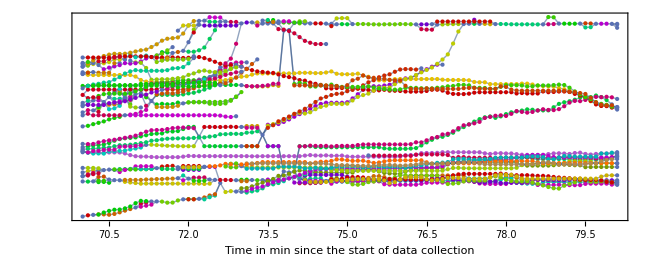

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
coloredGraph[g10,10000]
```

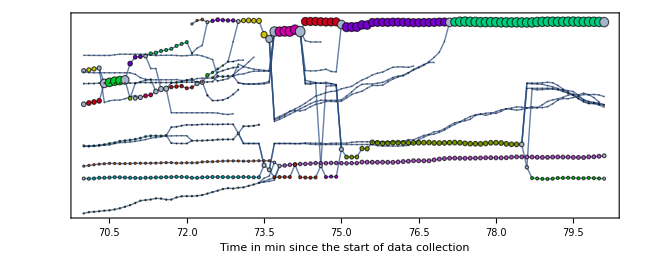

```mathematica
coloredGraph[g30,200]
```

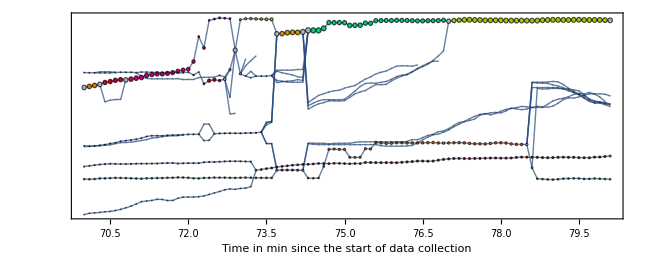

```mathematica
coloredGraph[g50,100]
```

#### Influence of Threshold

```mathematica
gstrict=FindFissionFusionGraph[700,800,0.99,dbScanHerds50LonelySheep];
```

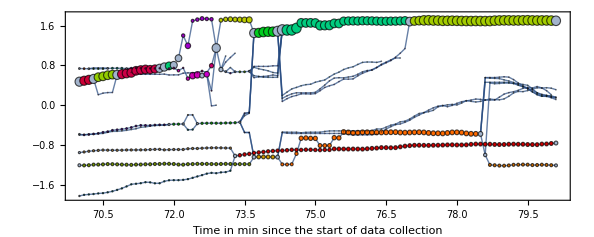

```mathematica
coloredGraph[gstrict,100]
```

```mathematica
animation=Animate[Show[metadataGraphic,Graphics[Circle[#,15]&/@DeleteMissing[rawCoordinates[[All,n]],1,2],PlotRange->RegionBounds[paddockRegion]],PlotRange->{{580401.,582573.},{6.562693*^6,6.564282*^6}}],{n,700,800,1}];
```

```mathematica
Export["/Users/katjad/Documents/Minerva/Capstone/Sheep/ActualMotionAnimation.mov",animation]
```

/Users/katjad/Documents/Minerva/Capstone/Sheep/ActualMotionAnimation.mov

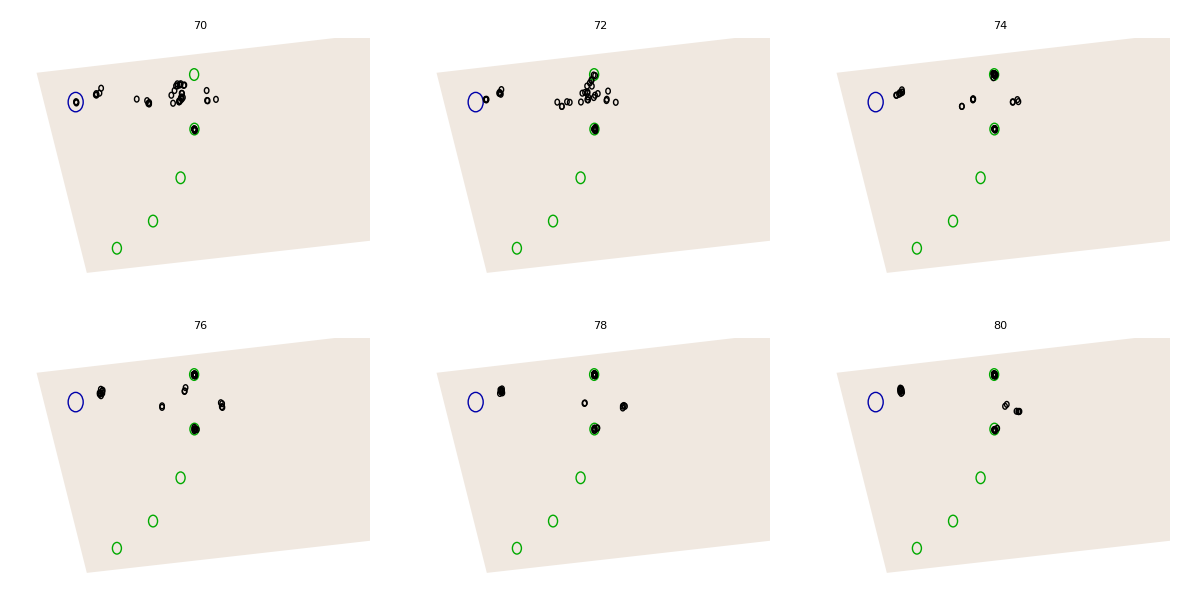

```mathematica
Grid[Partition[Table[Show[metadataGraphic,Graphics[Circle[#,15]&/@DeleteMissing[rawCoordinates[[All,n]],1,2],PlotRange->RegionBounds[paddockRegion]],PlotRange->{{580401.,582573.},{6.562693*^6,6.563882*^6}},PlotLabel->n/10],{n,700,800,20}],3]]
```

### Group Network Example Two

```mathematica
g10ExampleTwo=FindFissionFusionGraph[150000,150200,0.8,dbScanHerds10LonelySheep];
```

```mathematica
g30ExampleTwo =FindFissionFusionGraph[150000,150200,0.8,dbScanHerds30LonelySheep];
```

```mathematica
g50ExampleTwo=FindFissionFusionGraph[150000,150200,0.8,dbScanHerds50LonelySheep];
```

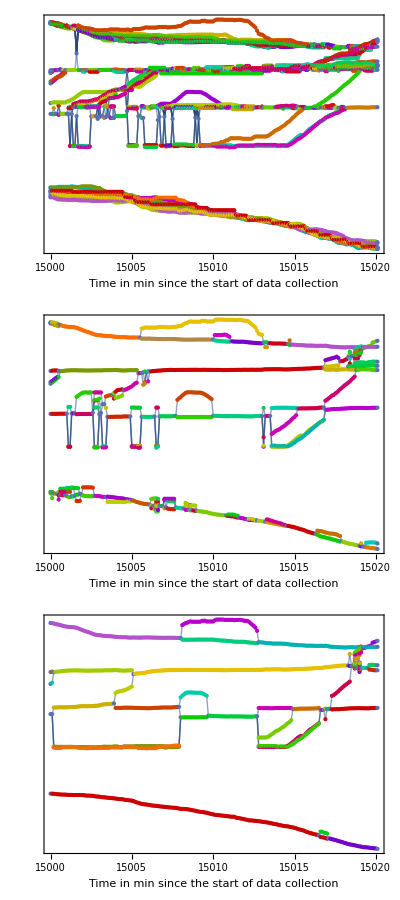

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Column[{coloredGraph[g10ExampleTwo,100],coloredGraph[g30ExampleTwo,100],coloredGraph[g50ExampleTwo,100]}]
```

```mathematica
Animate[Show[metadataGraphic,Graphics[Circle[#,15]&/@DeleteMissing[rawCoordinates[[All,n]],1,2],PlotRange->RegionBounds[paddockRegion]]],{n,150000,150200,1}]
```

## Personality data analysis

### Flight Initiation Distance

```mathematica
rawIDs2=Import["/Users/katjad/Documents/Github/SheepCapstone/ids.csv","Numeric"->False];
```

```mathematica
indexToEartag2=AssociationThread[Range[51],rawIDs2[[2;;,2]]];
```

```mathematica
eartagsToFID=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/IDmatching/eartagsToFID.mx"];
```

```mathematica
indexToFID=indexToEartag2/.eartagsToFID;
```

```mathematica
indexToMeanFID = MapAt[Mean,indexToFID,All]/.Mean["NA"]->"NA";
```

```mathematica
personalityHerds=dbScanHerds50/.indexToMeanFID/."NA"->Missing[];
```

```mathematica
averagePersonality=Mean/@DeleteCases[DeleteCases[Catenate[personalityHerds[[All,1;;-2]]],Missing[],2],{}];
```

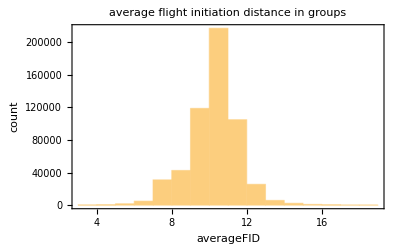

```mathematica
Histogram[averagePersonality,{1},Frame->True,FrameLabel->{"averageFID","count"},PlotLabel->"average flight initiation distance in groups"]
```

```mathematica
groupStability50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/groupStability50.mx"];
```

#### Time Alone

```mathematica
groupToTimeAlone=Length/@KeySelect[SortBy[groupStability50,Length],Length[#]==1&][[;;51]];
```

```mathematica
indexToTimeAlone=Association[#->groupToTimeAlone[{#}]&/@Range[51]];
```

```mathematica
FIDTimeAlone=DeleteCases[Table[{indexToMeanFID[x],indexToTimeAlone[x]},{x,51}],{"NA",_}];
```

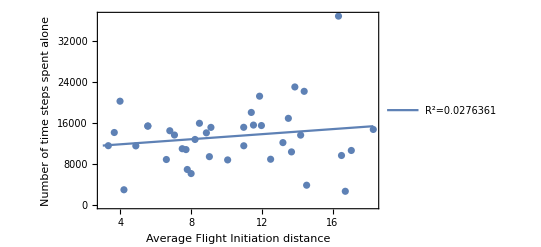

```mathematica
ResourceFunction["RegressionListPlot"][FIDTimeAlone,Frame->True,FrameLabel->{Style["Average Flight Initiation distance",Medium],Style["Number of time steps spent alone",Medium]},"DisplayRSquared"->True]
```

#### Average Group Size

```mathematica
indexToGroupLengths50=Merge[Function[ts,Catenate[Function[g,Function[s,s->Length[g]]/@g]/@ts]]/@dbScanHerds50LonelySheep,Identity];
```

```mathematica
indexToMeanGroupLength50 = MapAt[Mean,indexToGroupLengths50,All];
```

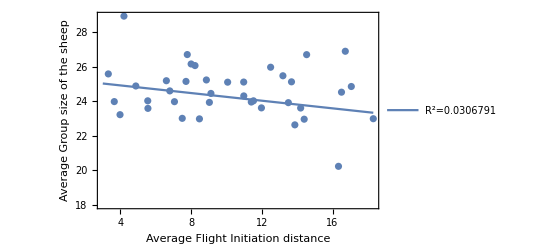

```mathematica
ResourceFunction["RegressionListPlot"][DeleteCases[Table[{indexToMeanFID[x],indexToMeanGroupLength50[x]//N},{x,51}],{"NA",_}],Frame->True,FrameLabel->{Style["Average Flight Initiation distance",Medium],Style["Average Group size of the sheep",Medium]},"DisplayRSquared"->True]
```

#### Group Stability

```mathematica
meanFIDToStability=DeleteCases[KeyValueMap[{Mean[DeleteCases[#1/.indexToMeanFID,"NA"]],(Mean[#2]+1)*6}&,Association[groupStability50]],{Mean[{}],_}];
```

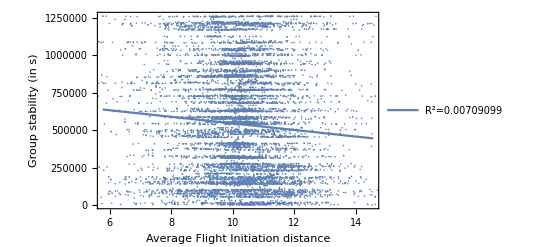

```mathematica
ResourceFunction["RegressionListPlot"][meanFIDToStability,Frame->True,FrameLabel->{Style["Average Flight Initiation distance",Medium],Style["Group stability (in s)",Medium]},"DisplayRSquared"->True]
```

### Exploration Tendency

#### Data Import

```mathematica
explorationRaw=Import["/Users/katjad/Documents/Github/SheepCapstone/buckets.csv","Numeric"->False];
```

```mathematica
flagToET=#[[2]]->Length[DeleteCases[#[[9;;71-LengthWhile[Reverse[#],Function[x,x==="NA"]]]],"NA"]]/3&/@explorationRaw[[2;;]];
```

Part::take: Cannot take positions 9 through 7 in {29,199,1,1,2018-03-09,NA,Started 10 sec before vid starts,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,«21»}.

```mathematica
eartagToFlags= ToString/@Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/IDmatching/earflags.mx"];
```

```mathematica
indexToEartag=AssociationThread[Range[51],rawIDs[[2;;,2]]];
```

```mathematica
flagtoMeanET=KeySort[Merge[flagToET,N[Mean[#]]&]];
```

```mathematica
indexToFlag=indexToEartag/.eartagToFlags;
```

```mathematica
indexToMeanET=indexToFlag/.flagtoMeanET;
```

```mathematica
flagToListET=KeySort[Merge[flagToET,#&]];
```

#### General Distribution

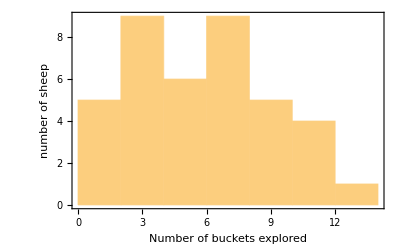

```mathematica
Histogram[Values[indexToMeanET],Frame->True,FrameLabel->{"Number of buckets explored","number of sheep"}]
```

#### Time Spent alone

```mathematica
groupStability50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/groupStability50.mx"];
```

```mathematica
groupToTimeAlone=Length/@KeySelect[SortBy[groupStability50,Length],Length[#]==1&][[;;51]];
```

```mathematica
indexToTimeAlone=Association[#->groupToTimeAlone[{#}]&/@Range[51]];
```

```mathematica
ETTimeAlone=DeleteCases[Table[{indexToMeanET[x],indexToTimeAlone[x]},{x,51}],{"NA",_}];
```

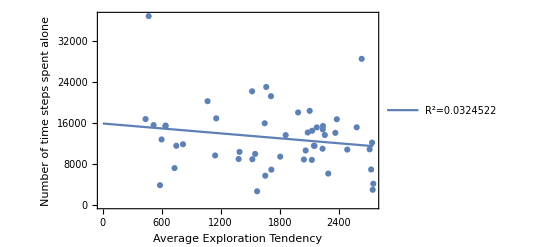

```mathematica
ResourceFunction["RegressionListPlot"][ETTimeAlone,Frame->True,FrameLabel->{Style["Average Exploration Tendency",Medium],Style["Number of time steps spent alone",Medium]},"DisplayRSquared"->True]
```

#### Average Group Size

```mathematica
indexToGroupLengths50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/indexToGroupLengths50.mx"];
```

```mathematica
indexToMeanGroupLength50 = MapAt[Mean,indexToGroupLengths50,All];
```

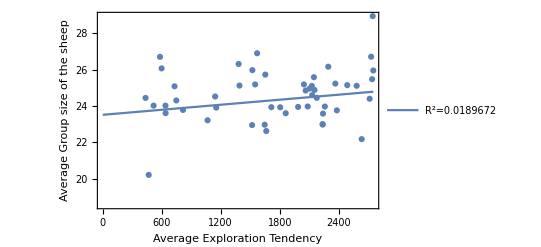

```mathematica
ResourceFunction["RegressionListPlot"][DeleteCases[Table[{indexToMeanET[x],indexToMeanGroupLength50[x]//N},{x,51}],{"NA",_}],Frame->True,FrameLabel->{Style["Average Exploration Tendency",Medium],Style["Average Group size of the sheep",Medium]},"DisplayRSquared"->True]
```

## Fission-Fusion Events

### Locations

```mathematica
FullStabilityGraph50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/FullStabilityGraph.mx"];
```

```mathematica
mergingEvents =Select[VertexList[FullStabilityGraph50],VertexInDegree[FullStabilityGraph50,#]≥2&];
```

```mathematica
splittingEvents =Select[VertexList[FullStabilityGraph50],VertexOutDegree[FullStabilityGraph50,#]≥ 2&];
```

```mathematica
mergingCoordinates =Mean[rawCoordinates[[#[[1]],#[[2]]]]]&/@mergingEvents;
```

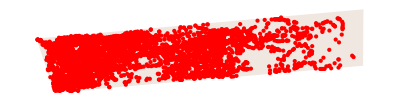

```mathematica
Show[metadataGraphic,Graphics[Style[Point[mergingCoordinates],Red]]]
```

```mathematica
splittingCoordinates=Mean[rawCoordinates[[#[[1]],#[[2]]]]]&/@splittingEvents;
```

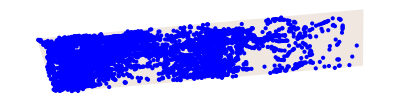

```mathematica
Show[metadataGraphic,Graphics[Style[Point[splittingCoordinates],Blue]]]
```

```mathematica
allCoordinates=Mean[rawCoordinates[[#[[1]],#[[2]]]]]&/@VertexList[FullStabilityGraph50];
```

```mathematica
splittingArray=BinCounts[splittingCoordinates,{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

```mathematica
mergingArray=BinCounts[mergingCoordinates,{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

```mathematica
allCoordinatesArray=BinCounts[allCoordinates,{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

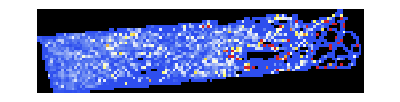

```mathematica
Show[{
metadataGraphic,Graphics[Raster[Map[If[#===Indeterminate,{0,0,0,0},Append[List@@ColorData["TemperatureMap"][#*10],0.8]]&,Transpose[Quiet[splittingArray/allCoordinatesArray]],{2}],Transpose[RegionBounds[paddockRegion]]]]
}]
```

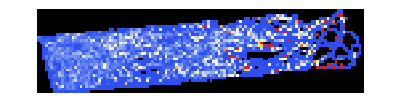

```mathematica
Show[{
metadataGraphic,Graphics[Raster[Map[If[#===Indeterminate,{0,0,0,0},Append[List@@ColorData["TemperatureMap"][#*10],0.8]]&,Transpose[Quiet[mergingArray/allCoordinatesArray]],{2}],Transpose[RegionBounds[paddockRegion]]]]
}]
```

### Splitting Events

#### Distance

```mathematica
splittingEvents50 =Select[VertexList[FullStabilityGraph50],VertexOutDegree[FullStabilityGraph50,#]=== 2&];
```

```mathematica
stablegroup[g_]:=ConnectedComponents[UndirectedGraph[Subgraph[g,Select[VertexList[g],VertexDegree[g,#]===2&]]]]
```

```mathematica
fullgroups50=stablegroup[FullStabilityGraph50];
```

```mathematica
groupsAssoc50=Association[First[#]->#&/@fullgroups50];
```

```mathematica
groupPositions[membersTime_]:=Mean[DeleteMissing[rawCoordinates[[membersTime[[1]],Last[membersTime]]]]]
```

```mathematica
paths=GeneralUtilities`MonitoredMap[Function[split,Catch[EuclideanDistance@@@Map[groupPositions,
Transpose[#[[All,;;UpTo[Min[Length/@#]]]]&@Lookup[
groupsAssoc50,
VertexOutComponent[FullStabilityGraph50,split,{1}],
Throw[Nothing]]],
{2}]]],splittingEvents50];
```

```mathematica
Rasterize[ListLinePlot[Select[paths,Length[#]>10&],PlotStyle->Directive[Black,Opacity[0.5],Thin],Frame->True,FrameLabel->{"Time in steps since splitting","Distance in m"}]]
```

-Graphics-

```mathematica
pathsFromZero=#-First[#]&/@paths;
```

```mathematica
Rasterize[ListLinePlot[Select[pathsFromZero,Length[#]>10&],PlotStyle->Directive[Black,Opacity[0.5],Thin],Frame->True,FrameLabel->{"Time in steps since splitting","Distance in m"}]]
```

-Graphics-

#### Angle

### Merging Events

#### Distance

#### Angle

## Movement Model

### Brownian Motion Model

```mathematica
paddockMemberQ=RegionMember[paddockRegion];
```

```mathematica
RandomMotion[position_,radius_,steps_]:=NestList[Module[{v},
v=RandomPoint[Circle[#,radius]];
While[!paddockMemberQ[v],v=RandomPoint[Circle[#,radius]]];v]&,
position,steps];
```

```mathematica
example = RandomMotion[RandomPoint[paddockRegion],50,500];
```

```mathematica
nullModelDataSet = Table[RandomMotion[RandomPoint[paddockRegion],50,100],51];
```

```mathematica
Dimensions[nullModelDataSet]
```

{51,101,2}

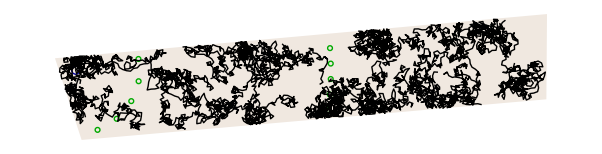

```mathematica
Show[{metadataGraphic,Graphics[Line[nullModelDataSet]]}]
```

```mathematica
dbScanClusters[data_,time_,radius_]:=
Module[{positions,rawClusters,outliers},
positions=DeleteMissing[MapIndexed[#1->#2[[1]]&,data[[All,time]]],1,3];
rawClusters=FindClusters[positions,Method->{"DBSCAN","NeighborhoodRadius"->radius,"DropAnomalousValues"->True},DistanceFunction->EuclideanDistance];
outliers=Complement[Values[positions],Flatten[rawClusters]];
Append[rawClusters,outliers]]
```

```mathematica
nullModelDBSCAN50=DeleteCases[Table[dbScanClusters[nullModelDataSet,x,50],{x,1,Length[nullModelDataSet[[1]]]}],{}];
```

```mathematica
FindRulesFromTo[first_,second_,firstindex_,threshold_]:=
Module[{r},
r=Reap[
Table[If[(Length[c1]-Length[Complement[c1,c2]])/Length[c1]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]];If[(Length[c2]-Length[Complement[c2,c1]])/Length[c2]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]],{c1,first},{c2,second}]];
If[Flatten[DeleteCases[r,{Null},2]]==={},{},DeleteDuplicates[r[[2,1]]]
]]
```

```mathematica
FindFissionFusionGraph[tmin_,tmax_,threshold_]:=Graph[Catenate[Table[FindRulesFromTo[nullModelDBSCAN50[[a]],nullModelDBSCAN50[[a+1]],a,threshold],{a,tmin,tmax}]]]
```

```mathematica
g=FindFissionFusionGraph[1,99,0.8];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

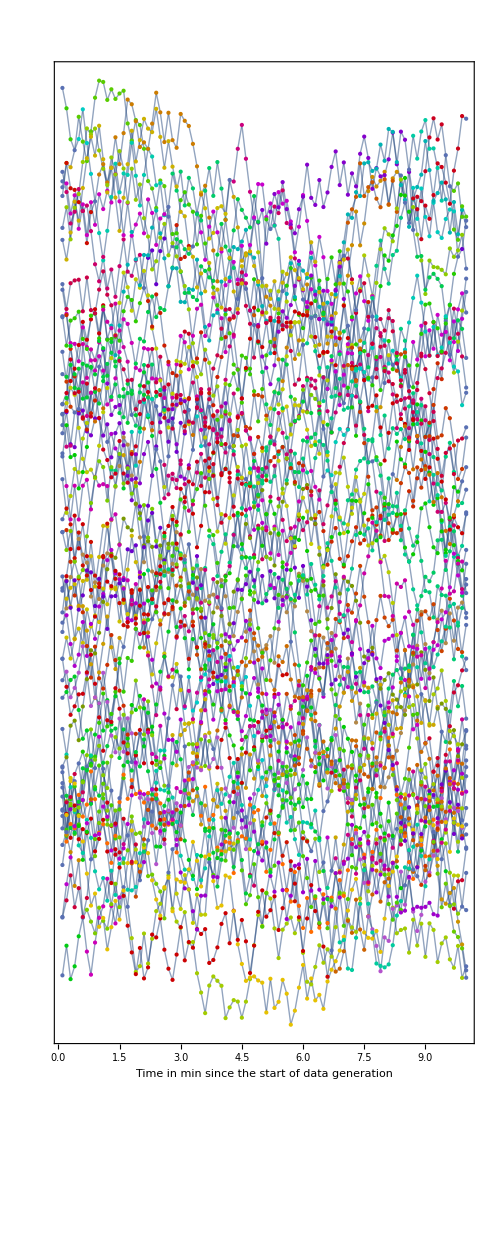

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
HighlightGraph[Graph[g,VertexSize->(#->Length[First[#]]*15&/@VertexList[g]),VertexCoordinates->(#->{Last[#]/10,nullModelDataSet[[First[#][[1]],Last[#]]][[2]]}&/@VertexList[g]),Frame->True,FrameTicks->{True,False},EdgeShapeFunction->"Line",FrameLabel->{Style["Time in min since the start of data generation",Medium],None}],ConnectedComponents[UndirectedGraph[Subgraph[g,Select[VertexList[g],VertexDegree[g,#]===2&]]]]]
```

### Null-Model Two: Couzin(2002)

### Model